#### Scheme

```mathematica
Block[{n=3,cnot,ah,block,split,bracket,obs,out,col},
SeedRandom[0];
obs=RandomChoice[{"X","Y","Z"},2^n];
out=RandomChoice[{"+","-"},2^n];
col=<|"X"->Cyan,"Y"->Magenta,"Z"->Yellow,"+"->Red,"-"->Blue|>;
(out[[#]]=out[[First@#]])&@Flatten@Position[obs,"Z"];
cnot[{i_,j_},l_]:={Line[{{l,-i},{l,-j-0.3}}],AbsolutePointSize[6],Point[{l,-i}],Circle[{l,-j},0.35]};
ah=Arrowheads[{{0.01,Automatic,Graphics[Line[Offset/@{{-3,-2},{0,0},{-3,2}}]]}}];
block[col_,txt_,causal_:False]:={{Lighter[col,0.8],Rectangle[{-1,-0.5},{1,0.5}]},If[causal,{{Lighter[col,0.5],Triangle[{{-1,-0.5},{1,-0.5},{-1,0.5}}]}},Nothing],
Line[{{-1,-0.5},{1,-0.5},{1,0.5},{-1,0.5},{-1,-0.5}}],{Text[Style[txt,LineSpacing->{0,14}]]}};
split=Block[{l=0.3,a=0.1},Scale[BSplineCurve[{{0,-a},{0,0},{a,0},{l-a,0},{l,0},{l,a}}],{#,1},{0,0}]&/@{-1,1}];
bracket[{x1_,x2_},y_]:=Block[{a=0.2,xm=(x1+x2)/2},{AbsoluteThickness[1],Scale[BSplineCurve[{{x1,y+a},{x1,y},{x1+a,y},{xm-a,y},{xm,y},{xm,y-a}}],{#,1},{xm,y}]&/@{1,-1}}];
Graphics[{Table[Translate[{Line[{{-1,0},{n+1,0}}],Block[{a=0.35},Translate[Scale[{{Lighter[col[Reverse[obs][[i]]],0.5],Polygon[{{-1,-1},{-1,1},{1,1},{1,-1}}]},AbsoluteThickness[1.2],Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}],Circle[{0,-1},1,{0,π}],Line[{{0,-1},{1,1}}]},a,{0,0}],{n+1+a,0}]]},{0,-i}],{i,2^n}],{Table[cnot[{i,i+2^(n-l)},l],{l,n},{i,1,2^n,2^(n-l+1)}]},
Translate[Block[{a=0.5},{{EdgeForm[Black],White,Rectangle[{-a,-a},{a,a},RoundingRadius->0.5a]},Text[Style["H",FontFamily->"CMU Sans Serif"],{0,0}]}],{0,-1}],
Table[{Text["\!\(|0⟩\)",{-1,-i},{1.2,0}]},{i,2^n}],
Text[Style["randomized\nmeasurements",LineSpacing->{0,12}],{n+1.7,-(2^n+1)/2},{0,-1},{0,-1}],
{AbsoluteThickness[1],
{bracket[{-2.3,n+0.7},-2^n-0.75],Text["cat",{0.8,-2^n-1.5}]},
Translate[{ah,
Arrow[{0,-#}&/@{(2^n+2)/2,2^n}],Arrow[{0,-#}&/@{(2^n)/2,1}],Text["\!\(N\)",{0,-(2^n+1)/2},{0,0.2}]},{-2.7,0}],
Text["(a) Quantum circuit",{-3,0},{-1,0}]},
Translate[{
Translate[{Text[Style["\!\(x\)",Bold],{0,2^n+1}],{GrayLevel[0.1],Rectangle[{-0.5,0.6},{0.5,2^n+0.6},RoundingRadius->0.2]},
Table[{col[obs[[i]]],Text[obs[[i]],{0,i}]},{i,2^n}]},{-1,0}],
Text["→",{0,#}]&/@Range[2^n],
Translate[{Text[Style["\!\(y\)",Bold],{0,2^n+1}],
{GrayLevel[0.9],Rectangle[{-0.5,0.6},{0.5,2^n+0.6},RoundingRadius->0.2]},Table[{col[out[[i]]],Text[out[[i]],{0,i}]},{i,2^n}]},{1,0}],
bracket[{-1.6,1.6},0.2],Text["classical shadow",{0,-0.6}]},{n+5.5,-2^n-1}],
Text["⇒",{n+8,-(2^n+1)/2}],
Translate[Scale[{Arrowheads[{{0.001,1,Graphics[{Dashing[{}],Line[Offset/@{{-4,-3},{-1,0},{-4,3}}]}]}}],Translate[{{Text["\!\(x\)",{0,-0.8},{0,0.8}],Arrow[{0,#}&/@{-0.8,-0.5}],Translate[{Line[{0,#}&/@{-0.2,-0.1}],split,Translate[Arrow[{0,#}&/@{0,0.1}],{# 0.3,0.1}]&/@{1,-1}},{0,0.7}],
{Text["\!\(μ\_z\)",{-0.3,1.1}],Text["\!\(σ\_z\)",{0.3,1.1}],Text["\!\(p\_θ(z|x)\)",{0,1.5}]},
block[Red,"transformer\nencoder"]}},{-1.5,0}],
{{Dashed,Gray,Arrow@BSplineCurve[{{-0.8,1.5},{-0.25,1.5},{0,1.5},{0,1.25},{0,0.95}}],
Text[Style["sample",12],{-0.4,1.7}]},
Text["\!\(z\)",{0,0.75}],Arrow@BSplineCurve[{{0,0.55},{0,0.25},{0,0},{0.25,0},{0.5,0}}]},
Translate[{{Text["\!\(y\)",{0,-0.8},{0,0.8}],Arrow[{0,#}&/@{-0.8,-0.5}],Arrow[{0,#}&/@{0.5,0.8}],Text["\!\(p\_θ(y|z)\)",{0,0.8},{0,-0.8}],
block[Blue,"transformer\ndecoder",True]}},{1.5,0}],
Text["\!\(p\_θ(y|x)=∫\_z p\_θ(y|z)p\_θ(z|x)\)",{0.3,-1.5}],
Text["(b) Language model",{0,2.08}]
},2.5,{0,0}],{n+15,-(2^n+2.5)/2}]},PlotRange->{{-3,24.5},{-2^n-2,0.6}},ImageSize->440]]
```

-Graphics-

#### β-VAE

```mathematica
Block[{braket,block},
block[col_,txt_,causal_:False]:={{Lighter[col,0.8],Rectangle[{-1,-0.5},{1,0.5}]},If[causal,{{Lighter[col,0.5],Triangle[{{-1,-0.5},{1,-0.5},{-1,0.5}}]}},Nothing],
Line[{{-1,-0.5},{1,-0.5},{1,0.5},{-1,0.5},{-1,-0.5}}],{Text[Style[txt,LineSpacing->{0,14}]]}};
braket=Block[{l=0.3,a=0.1},Scale[BSplineCurve[{{0,-a},{0,0},{a,0},{l-a,0},{l,0},{l,a}}],{#,1},{0,0}]&/@{-1,1}];
Graphics[{Arrowheads[{{0.001,Automatic,Graphics[{Dashing[{}],Line[Offset/@{{-3,-3},{0,0},{-3,3}}]}]}}],Translate[{{Text["\!\(x\)",{0,-0.8},{0,0.8}],Arrow[{0,#}&/@{-0.8,-0.5}],Translate[{Line[{0,#}&/@{-0.2,-0.1}],braket,Translate[Arrow[{0,#}&/@{0,0.1}],{# 0.3,0.1}]&/@{1,-1}},{0,0.7}],
{Text["\!\(μ\_z\)",{-0.3,1.1}],Text["\!\(σ\_z\)",{0.3,1.1}],Text["\!\(log p\_θ(z|x)\)",{0,1.5}]},
block[Red,"transformer\nencoder"]}},{-1.5,0}],
{{Dashed,Arrow@BSplineCurve[{{-0.5,1.5},{-0.25,1.5},{0,1.5},{0,1.25},{0,0.95}}]},
Text["\!\(z\)",{0,0.75}],Arrow@BSplineCurve[{{0,0.55},{0,0.25},{0,0},{0.25,0},{0.5,0}}]},
Translate[{{Text["\!\(y\)",{0,-0.8},{0,0.8}],Arrow[{0,#}&/@{-0.8,-0.5}],Arrow[{0,#}&/@{0.5,0.8}],Text["\!\(log p\_θ(y|z)\)",{0,0.8},{0,-0.8}],
block[Blue,"transformer\ndecoder",True]}},{1.5,0}]
},ImageSize->200]]
```

-Graphics-

#### Transformer

```mathematica
Block[{r=0.3,w=4,ah,add,qkv,textbox,roundline,base,encoder,decoder,outproj,bottleneck},
ah=Arrowheads[{{0.001,1,Graphics[{Dashing[{}],Line[Offset/@{{-4,-3},{-1,0},{-4,3}}]}]}}];
add[pos_:{0,0},θ0_:0]:=Translate[{{EdgeForm[Directive[Black,AbsoluteThickness[1]]],White,Disk[{0,0},r]},{AbsoluteThickness[1],Rotate[Line[{0.6 # r,0}&/@{-1,1}],# π/2+θ0,{0,0}]&/@{0,1}}},pos];
qkv=Text[Style[#1,10,Gray],{#2,1},{-2,1}]&@@@{{"Q",1.5},{"K",0},{"V",-1.5}};
textbox[col_,txt_,pos_:{0,0},masked_:False]:=Block[{h},
h=StringCount[txt,"\n"]+1;
Translate[{{EdgeForm[Black],Lighter[col,0.8],Rectangle[{-2.5,-h/2},{2.5,h/2},RoundingRadius->0.3]},Text[Style[txt,LineSpacing->{0,14}],{0,0}]},pos]];
roundline[pts_,r_:0.4]:=BSplineCurve[Flatten[Riffle[List/@pts,Thread[Table[(#1+r Normalize[#2-#1])&@@@Thread[Through[f[{Most,Rest}][pts]]],{f,{Identity,Reverse}}]]],1]];
base={{Arrow[{{0,0},{(w-r)#,0}}]&/@{-1,1},textbox[Orange,"Positional\nEncoding",{0,0}]},
Translate[{Translate[{Text["Observables x",{0,-3},{0,1}],Arrow[Line[{0,#}&/@{-3,-2}]],textbox[Red,"Token\nEmbedding",{0,-1}]},{0,-1.5}],
Arrow[{{0,-1.5},{0,-r}}],add[{0,0}],Line[{{0,r},{0,1.5}}]},{-w,0}],
Translate[{Translate[{Text[Style["Outcomes y\n(shifted right)",LineSpacing->{0,14}],{0,-3},{0,1}],Arrow[Line[{0,#}&/@{-3,-2}]],textbox[Red,"Token\nEmbedding",{0,-1}]},{0,-1.5}],
Arrow[{{0,-1.5},{0,-r}}],add[{0,0}],Line[{{0,r},{0,1.5}}]},{w,0}]};
encoder={{EdgeForm[Directive[Black,Dashed]],GrayLevel[0.95],Rectangle[{-4,0},{3,11},RoundingRadius->0.5]},
{Arrow[{0,#}&/@{0,1}],Arrow[roundline[{{0,0.5},{-3.5,0.5},{-3.5,5.5},{-r,5.5}}]],textbox[Yellow,"Norm",{0,1.5}],
Translate[{Arrow[roundline[{{0,0.4},{-1.5,0.4},{-1.5,1}}]],
Arrow[{0,#}&/@{0,1}],Arrow[roundline[{{0,0.4},{1.5,0.4},{1.5,1}}]],
qkv},{0,2}],
textbox[Green,"Multi-Head\nAttention",{0,4}],
Translate[Arrow[{0,#}&/@{0,1.5}],{0,5}],
add[{0,5.5}],
Arrow[roundline[{{0,6},{-3.5,6},{-3.5,10.5},{-r,10.5}}]],
textbox[Yellow,"Norm",{0,7}],
Translate[Arrow[{0,#}&/@{0,0.5}],{0,7.5}],
textbox[Cyan,"Feed\nForward",{0,9}],
Translate[Line[{0,#}&/@{0,1}],{0,10}],
add[{0,10.5}]},
Text["\!\(L×\)",{-4.2,5.5},{1,0}]};
decoder={{EdgeForm[Directive[Black,Dashed]],GrayLevel[0.95],Rectangle[{-3,0},{4,17.5},RoundingRadius->0.5]},
{Arrow[{0,#}&/@{0,1}],Arrow[roundline[{{0,0.5},{3.5,0.5},{3.5,6.5},{r,6.5}}]],textbox[Yellow,"Norm",{0,1.5}],
Translate[{Arrow[roundline[{{0,0.4},{-1.5,0.4},{-1.5,1}}]],
Arrow[{0,#}&/@{0,1}],Arrow[roundline[{{0,0.4},{1.5,0.4},{1.5,1}}]],
qkv},{0,2}],
textbox[Green,"Masked\nMulti-Head\nAttention",{0,4.5}],
Translate[Arrow[{0,#}&/@{0,1.5}],{0,6}],
add[{0,6.5}],
Arrow[roundline[{{0,7},{3.5,7},{3.5,12},{r,12}}]],
textbox[Yellow,"Norm",{0,8}],
Translate[{Arrow[roundline[{{-3,0.4},{-1.5,0.4},{-1.5,1}}]],
Arrow[roundline[{{-1.7,0.4},{0,0.4},{0,1}}]],Arrow[roundline[{{0,0},{0,0.4},{1.5,0.4},{1.5,1}}]],
qkv},{0,8.5}],
textbox[Green,"Multi-Head\nAttention",{0,10.5}],
Translate[Arrow[{0,#}&/@{0,1.5}],{0,11.5}],
add[{0,12}],
Arrow[roundline[{{0,12.5},{3.5,12.5},{3.5,17},{r,17}}]],
textbox[Yellow,"Norm",{0,13.5}],
Translate[Arrow[{0,#}&/@{0,0.5}],{0,14}],
textbox[Cyan,"Feed\nForward",{0,15.5}],
Translate[Line[{0,#}&/@{0,1}],{0,16.5}],
add[{0,17}]},
Text["\!\(×L\)",{4.2,9},{-1,0}]};
outproj={Arrow[{0,#}&/@{0,0.5}],textbox[Blue,"Linear",{0,1}],
Translate[Arrow[{0,#}&/@{0,0.5}],{0,1.5}],
textbox[Purple,"Softmax",{0,2.5}],
Translate[Arrow[{0,#}&/@{0,1}],{0,3}],
Text["\!\(p\_θ(y|z)\)",{0,4},{0,-1}]};
bottleneck={Arrow[{0,#}&/@{0,0.5}],textbox[Blue,"Linear",{0,1}],
Translate[{Text["\!\(ξ\[Distributed]𝒩(0,1)\)",{-2,1.5},{-0.45,0}],Arrow[roundline[{{-3,1},{-3,0},{w,0},{w,-1}}]],
Text["\!\(z\)",{w,-1.5}]},{0,4}],
Translate[{Arrow[{0,#}&/@{0,0.7}],Text["mean \!\(μ\_z\)",{0,1.}],
Arrow[{0,#}&/@{1.5,2.5-r}],add[{0,2.5}]},{1.5,1.5}],
Translate[{Arrow[{0,#}&/@{0,0.7}],Text["std \!\(σ\_z\)",{0,1.}],Arrow[{0,#}&/@{1.5,2.5-r}],add[{0,2.5},π/4]},{-1.5,1.5}],
roundline[{{w,2},{w,-2.1},{2w-3,-2.1}}],
Text["\!\(p\_θ(z|x)=𝒩(μ\_z,σ\_z)\)",{0,7}]};
Graphics[{ah,
Translate[base,{0,-1.5}],
Translate[encoder,{-w,0}],
Translate[bottleneck,{-w,11}],
Translate[decoder,{w,0}],
Translate[outproj,{w,17.5}]},ImageSize->320]]
```

-Graphics-

#### Framework

```mathematica
Block[{asset,bit,opblend,wave,opsty},
asset=<|"alive"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{39.26,60.69},{40.54,63.09},{42.44,65.11},{44.76,66.53},{46.59,63.73},{46.93,61.34},{47.28,57.83},{47.59,54.7},{48.02,49.41},{44.28,44.83},{42.,42.23},{43.,40.47},{43.67,32.74},{43.82,28.96},{43.52,25.17},{42.75,21.46},{42.2,18.6},{41.06,15.73},{41.49,13.84},{41.82,12.37},{41.60,10.89},{40.14,10.17},{39.94,10.07},{39.72,9.993},{39.49,9.95},{38.3,9.636},{37.04,10.08},{36.31,11.07},{36.74,9.83},{36.86,8.07},{36.06,7.43},{34.78,6.503},{33.1,6.328},{31.65,6.97},{30.32,7.77},{30.,8.63},{29.,9.89},{25.73,8.803},{22.22,8.623},{18.86,9.37},{16.36,10.05},{13.75,10.19},{11.19,9.78},{9.466,9.568},{6.53,8.66},{6.33,7.33},{6.13,6.},{8.73,5.8},{9.42,3.65},{9.65,2.923},{9.32,2.136},{8.64,1.79},{7.78,1.34},{6.93,1.37},{5.3,2.16},{2.43,3.53},{1.17,5.82},{1.57,8.46},{2.013,10.11},{3.054,11.54},{4.49,12.46},{7.73,14.38},{11.14,14.75},{14.69,14.81},{14.17,17.21},{12.57,21.94},{14.92,27.98},{17.17,33.76},{22.61,38.57},{26.2,43.44},{26.61,44.11},{26.59,44.97},{26.14,45.62},{24.83,47.51},{22.77,51.69},{22.76,55.18},{22.87,59.},{23.81,62.76},{25.51,66.18},{27.91,65.01},{29.9,63.16},{31.24,60.85},{31.29,60.74},{32.85,61.14},{33.87,61.2},{35.68,61.31},{37.5,61.14},{39.26,60.69}}}],
JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{28.,48.97},{27.33,49.06},{26.85,49.66},{26.9,50.34},{26.9,51.34},{27.26,53.34},{29.15,53.89},{29.93,54.17},{30.81,54.03},{31.46,53.51},{32.54,52.68},{32.66,51.37},{32.7,50.08},{32.7,49.62},{32.81,49.54},{32.05,49.27},{30.75,48.84},{29.35,48.73},{28.,48.97}},{{42.77,49.12},{43.86,49.52},{43.86,50.28},{43.84,50.53},{43.81,51.94},{42.94,53.19},{41.62,53.7},{40.83,53.92},{39.99,53.67},{39.45,53.05},{38.53,52.2},{38.09,50.95},{38.26,49.71},{38.26,49.26},{38.54,48.87},{39.33,48.71},{40.49,48.57},{41.67,48.71},{42.77,49.12}}}]},
"dead"->{JoinedCurve[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{63.33, 23.69}, {65.85, 13.27}, {62.47, 9.69}, {60.32, 6.94}, {58.36, 4.55}, {55.33, 2.76}, {52.03, 2.09}, {49.30, 1.51}, {44.55, 1.27}, {42.87, 1.26}, {41.69, 1.25}, {40.37, 1.88}, {40.15, 2.94}, {39.96, 4.10}, {40.80, 4.80}, {41.78, 5.02}, {42.96, 5.27}, {43.85, 5.46}, {46.37, 5.86}, {48.06, 6.13}, {52.54, 6.53}, {55.24, 8.72}, {58.24, 11.19}, {59.44, 15.95}, {59.08, 15.72}, {58.34, 15.07}, {57.26, 14.32}, {54.13, 13.61}, {51.60, 13.19}, {49.99, 13.82}, {50.03, 13.43}, {50.13, 12.58}, {50.26, 10.57}, {47.95, 9.95}, {46.74, 9.65}, {45.49, 10.08}, {44.76, 11.08}, {45.18, 9.79}, {45.35, 8.09}, {44.46, 7.40}, {43.24, 6.52}, {41.56, 6.33}, {40.11, 6.97}, {38.75, 7.82}, {38.44, 8.63}, {37.46, 9.90}, {35.63, 12.57}, {32.49, 13.86}, {29.38, 13.34}, {28.01, 13.02}, {27.14, 10.29}, {23.69, 8.35}, {19.40, 6.25}, {11.36, 5.37}, {7.17, 6.66}, {6.71, 6.94}, {9.51, 10.38}, {11.52, 11.98}, {11.84, 12.23}, {10.26, 13.70}, {9.74, 15.76}, {9.40, 17.15}, {8.83, 19.60}, {9.06, 20.52}, {7.49, 20.94}, {1.16, 22.05}, {1.59, 22.72}, {6.06, 27.46}, {12.13, 30.36}, {17.08, 30.73}, {21.24, 31.15}, {24.02, 29.00}, {25.18, 29.88}, {28.92, 32.66}, {32.67, 34.71}, {36.06, 35.91}, {41.02, 37.57}, {45.23, 37.61}, {50.40, 36.49}, {58.91, 34.11}, {62.30, 27.24}, {63.33, 23.69}}}], JoinedCurve[{{{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}}, {{{14.81, 24.56}, {18.14, 21.59}}, {{17.08, 25.14}, {15.72, 20.96}}, {{17.35, 15.88}, {20.54, 12.98}}, {{19.57, 16.46}, {18.09, 12.46}}}]},
"neuron"->JoinedCurve[{{{1,4,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{56.68,24.8},{56.42,25.32},{56.2,25.85},{56.15,27.5},{56.36,33.72},{48.49,40.15},{44.9,42.79},{44.82,42.85},{43.6,43.73},{39.82,46.45},{23.34,53.72},{18.88,61.89},{16.3,67.35},{15.76,74.57},{16.68,81.33},{17.05,83.17},{18.08,83.79},{19.14,84.3},{21.58,85.51},{24.95,85.16},{29.36,82.59},{26.81,86.74},{24.54,87.83},{24.54,91.59},{24.54,96.12},{28.02,97.79},{31.25,100.9},{29.01,99.96},{22.49,98.04},{20.38,100.},{17.66,102.6},{18.15,105.7},{17.57,109.3},{16.36,106.4},{15.4,101.7},{12.14,100.2},{9.07,98.87},{4.79,100.8},{1.91,102.2},{4.26,99.36},{7.91,95.77},{7.73,92.51},{7.45,87.83},{3.57,86.18},{1.53,83.37},{4.09,84.37},{7.89,86.24},{10.73,85.09},{12.5,84.38},{13.47,82.81},{13.39,80.39},{13.46,73.91},{13.68,67.62},{16.68,61.52},{20.91,52.49},{38.6,45.1},{42.57,42.24},{43.77,41.37},{43.85,41.31},{46.98,39.01},{54.52,33.63},{54.45,27.7},{54.43,27.16},{54.41,26.77},{54.36,26.4},{54.33,26.03},{54.33,25.75},{54.27,25.47},{54.22,25.21},{54.17,24.95},{54.14,24.93},{54.09,24.79},{53.82,24.32},{53.49,23.9},{53.09,23.53},{52.63,23.24},{52.08,23.11},{51.54,23.17},{50.36,23.35},{49.54,24.9},{48.89,26.04},{48.27,27.39},{47.17,28.45},{45.81,29.04},{45.74,29.04},{45.62,29.04},{44.67,29.94},{43.5,30.59},{42.24,30.93},{42.06,30.26},{43.,30.01},{43.88,29.57},{44.65,28.97},{44.18,28.85},{43.71,28.73},{43.26,28.6},{43.09,28.56},{42.96,28.43},{42.93,28.26},{42.91,28.12},{42.97,27.97},{43.09,27.89},{43.5,27.89},{43.5,27.98},{43.97,28.12},{44.44,28.24},{44.91,28.35},{45.33,28.33},{45.74,28.23},{46.12,28.05},{46.93,27.58},{47.12,26.96},{47.75,26.05},{47.43,26.16},{47.09,26.21},{46.75,26.21},{45.82,26.67},{44.79,26.9},{43.75,26.87},{43.75,26.19},{44.52,26.21},{45.28,26.07},{45.99,25.79},{45.41,25.56},{44.84,25.29},{44.3,24.98},{44.65,24.39},{45.28,24.76},{45.95,25.06},{46.65,25.29},{47.45,25.27},{48.2,24.93},{48.75,24.35},{49.23,23.48},{49.92,22.73},{50.75,22.18},{50.69,22.18},{50.01,22.16},{49.34,22.25},{48.69,22.45},{47.61,23.07},{46.35,23.34},{45.11,23.22},{45.18,22.54},{46.03,22.62},{46.88,22.5},{47.67,22.18},{46.94,21.9},{46.24,21.54},{45.59,21.1},{45.97,20.53},{46.72,21.03},{47.55,21.42},{48.42,21.68},{49.11,21.42},{49.84,21.26},{50.57,21.18},{50.54,21.13},{50.51,21.08},{50.49,21.02},{50.31,20.29},{49.81,19.69},{49.13,19.37},{48.25,19.29},{47.68,18.93},{46.93,18.18},{46.25,17.69},{46.64,17.12},{47.2,17.52},{47.75,17.95},{48.27,18.4},{48.35,18.03},{48.4,17.64},{48.4,17.26},{48.41,16.73},{48.23,16.22},{47.9,15.81},{48.4,15.34},{48.85,15.87},{49.09,16.55},{49.08,17.25},{49.05,17.69},{49.12,18.13},{49.27,18.54},{50.43,19.03},{51.3,20.04},{51.6,21.27},{51.73,21.88},{52.6,21.9},{53.69,22.58},{54.78,23.26},{55.36,24.18},{55.42,24.03},{55.81,23.32},{56.12,22.57},{56.35,21.79},{56.49,20.24},{56.31,18.67},{55.8,17.19},{55.55,16.28},{55.17,15.41},{54.68,14.6},{54.43,14.27},{54.08,14.03},{53.68,13.9},{53.43,13.82},{52.55,13.73},{52.43,13.71},{52.3,13.69},{52.16,13.65},{52.04,13.59},{51.69,13.59},{50.82,13.74},{49.98,13.99},{49.18,14.36},{48.53,14.49},{47.91,14.67},{47.31,14.9},{46.73,15.17},{46.66,15.17},{46.38,14.54},{46.46,14.54},{47.,14.29},{47.55,14.07},{48.12,13.89},{47.93,13.76},{47.72,13.65},{47.51,13.56},{47.03,13.35},{46.56,13.14},{46.84,12.51},{47.31,12.72},{47.78,12.93},{48.13,13.06},{48.45,13.26},{48.73,13.52},{49.53,13.17},{50.36,12.91},{51.22,12.74},{50.5,12.08},{49.61,11.63},{48.65,11.45},{47.84,11.49},{47.04,11.64},{46.27,11.89},{46.04,11.24},{46.69,11.03},{47.36,10.88},{48.04,10.81},{47.82,10.61},{47.58,10.43},{47.33,10.27},{47.09,10.12},{46.83,9.986},{46.57,9.87},{45.91,9.54},{46.23,8.93},{46.87,9.25},{47.16,9.375},{47.44,9.525},{47.71,9.7},{48.13,9.976},{48.51,10.31},{48.84,10.7},{49.56,10.85},{50.56,11.13},{51.47,11.67},{52.2,12.41},{53.01,12.82},{53.44,12.84},{53.87,12.89},{54.3,12.97},{53.9,11.7},{53.33,10.5},{52.6,9.39},{52.16,8.851},{51.62,8.411},{51.,8.1},{50.19,7.79},{49.34,7.611},{48.47,7.57},{47.86,7.57},{47.42,7.647},{46.97,7.7},{46.52,7.73},{45.52,7.84},{45.43,7.16},{46.43,7.05},{46.76,7.05},{47.11,6.99},{47.43,6.94},{47.25,6.8},{47.,6.62},{46.65,6.39},{46.53,6.31},{46.37,6.22},{46.2,6.13},{46.03,6.04},{45.71,5.85},{45.52,5.71},{45.93,5.16},{46.09,5.27},{46.32,5.4},{46.54,5.53},{47.03,5.82},{47.44,6.073},{47.83,6.368},{48.18,6.7},{48.91,6.654},{49.65,6.714},{50.37,6.88},{50.11,6.263},{49.69,5.728},{49.15,5.33},{48.47,4.789},{47.7,4.372},{46.87,4.1},{46.55,4.1},{46.09,4.1},{45.18,4.1},{44.55,4.1},{44.2,4.1},{44.2,3.41},{46.,3.41},{45.79,3.081},{45.54,2.779},{45.26,2.51},{44.95,2.237},{44.62,1.996},{44.26,1.79},{44.02,1.65},{43.57,1.43},{43.49,1.36},{43.7,0.87},{43.77,0.93},{44.63,1.35},{44.85,1.45},{45.59,1.814},{46.21,2.388},{46.63,3.1},{47.75,3.397},{48.81,3.914},{49.73,4.62},{50.59,5.237},{51.24,6.103},{51.59,7.1},{52.35,7.622},{53.02,8.256},{53.59,8.98},{54.44,10.31},{55.05,11.78},{55.38,13.33},{55.38,13.33},{56.51,15.66},{56.85,16.56},{57.41,17.89},{57.69,19.32},{57.68,20.77},{57.59,22.16},{57.25,23.53},{56.68,24.8}}}],
"0"->Cases[ImportString[ExportString[Text[Style["0",FontFamily->"CMU Concrete"]],"PDF"],"PageGraphics"],_FilledCurve,∞],
"1"->Cases[ImportString[ExportString[Text[Style["1",FontFamily->"CMU Concrete"]],"PDF"],"PageGraphics"],_FilledCurve,∞]|>;
bit[col_,state_,blk_:0.4,bdy_:0.98]:=
Translate[Join[{EdgeForm[Directive[col,Opacity[bdy]]],Directive[col,Opacity[blk]]},asset[state]],{-2.4,-7.8}];
opblend[gs_,n_:10]:=Flatten[Table[gs,n],1]/.{Opacity[x_]:>Opacity[1-(1-x)^(1/n)]};
wave[{p1_,p2_}]:=Block[{sb=0.9,t,n},
t=p2-p1;n=Normalize[{{0,1},{-1,0}}.t];
{Arrowheads[{{0.001,Automatic,Graphics[Line[Offset/@{{-3,3},{0,0},{-3,-3}}]]}}],Arrow@Table[p1+x t+2Sin[π x/sb](Cos[10π x/sb])n UnitStep[sb-x],{x,0,1,0.01}]}];
opsty[col_,blk_:0.4,bdy_:0.98]:={col,{Opacity[blk],FilledCurve@@First@#},{Opacity[bdy],#}}&;
Graphics[{
(*background*){Block[{x1=-100,x2=100,y1=-30,y2=150},
{(*gradient*)Raster[{(1+Tanh[Range[-10,10,0.02]])/2},{{x1,y1},{x2,y2}}],
(*frame*){Black,Line[{{x1,y1},{x1,y2},{x2,y2},{x2,y1},{x1,y1}}]}}],
(*world labels*){(*Opacity[0.5],*)
(*quantum*){White,Text[Style["Quantum World",Bold,16],{-50,-20}]},
(*classical*){Black,Text[Style["Classical World",Bold,16],{50,-20}]}}},
(*quantum world*)Translate[{
{(*qubit*)Translate[{
(*atomic shell*){White,Rotate[Circle[{0,0},{8,16}],2 π#/3]&/@ Range[3]},
{(*spin*)AbsoluteThickness[1],opblend@{
Translate[Scale[bit[Pink,"0"],1.5],{2,-2}],
Translate[Scale[bit[Cyan,"1"],1.5],{-2,2}]}}},{0,95}]},
{(*entanglement*)White,AbsoluteThickness[2],AbsoluteDashing[6],BSplineCurve[{{-10,80},{-30,60},{-15,30}}]},
(*Schrodinger cat*)Translate[opblend@{
(*alive cat*)Translate[opsty[Pink]@asset["alive"],{-36.31,-11.07}],
(*dead cat*)Translate[opsty[Cyan]@asset["dead"],{-44.69,-11.20}]},{10,0}],
(*cat state*)Translate[{
(*cat state*){
(*alive state*)Translate[{
(*spin+cat*){AbsoluteThickness[1],Translate[Scale[bit[Pink,"0"],1.2],{-6,0}],Translate[Scale[Translate[opsty[Pink]@asset["alive"],{-36.31,-11.07}],0.2,{0,0}],{6,-5}]},(*ket symbol*){White,Line[{-12,#}&/@{-7,7}],Line[{12-0.3Abs[#],#}&/@{-7,0,7}]}},{-18,0}],
(*dead state*)Translate[{
(*spin+cat*){AbsoluteThickness[1],Translate[Scale[bit[Cyan,"1"],1.2],{-6,0}],Translate[Scale[Translate[opsty[Cyan]@asset["dead"],{-36.31,-11.07}],0.2,{0,0}],{4.5,-1}]},(*ket symbol*){White,Line[{-12,#}&/@{-7,7}],Line[{12-0.3Abs[#],#}&/@{-7,0,7}]}},{18,0}],
(*plus sign*){White,Text[Style["+",18],{0,0}]}},
(*title*){White,Text["Quantum superposition",{0,16}]}},{0,125}]},{-50,0}],
(*classical world*)Translate[{
(*eye*){Circle[{0,0},27],{Gray,Disk[{-12,0},12]},{Black,Disk[{-14,0},6]},{White,Translate[Rotate[Disk[{0,0},{2,3}],π/4],ReIm[-14+6Exp[ⅈ π/4]]]}},
(*neoron*)Translate[{
(*cell*){EdgeForm[Black],GrayLevel[0.9],FilledCurve@@asset["neuron"]},
(*neuclear*){Gray,Disk[{16,92.5},3.5]}},{-21,-15}],
(*emergent classicality*)Translate[{
(*cloud*)Line@Table[{15,10}ReIm[Exp[ⅈ θ]+0.1Exp[10 ⅈ θ]],{θ,0.,2π,0.01π}],
(*spin+cat*){AbsoluteThickness[1],Translate[Scale[bit[Black,"0"],1.2],{-6,0}],Translate[Scale[Translate[opsty[Black]@asset["alive"],{-36.31,-11.07}],0.2,{0,0}],{6,-5}]},
(*bubbles*){Circle[{-16,-11},4],Circle[{-25,-15},2]},
(*title*){Black,Text["Classical reality",{-10,16}]}},{30,105}]},{45,20}],
(*weak measurement*)Translate[{
(*dotted lines*){AbsoluteThickness[3],Yellow,Dashed,Table[Line[{{-14,1.2y},{14,0.8y}}],{y,-20,20,10}]},
(*text*)Translate[Block[{txt=Style["Randomized\nmeasurement\noutcomes",Bold,LineSpacing->{0,14}]},{{Black,Text[txt,ReIm[0.8Exp[ⅈ 2π #/48]]]&/@Range[48]},{Yellow,Text[txt]}}],{0,45}]},{0,20}]},PlotRangePadding->None,ImageSize->300]]
```

-Graphics-

##### Draft

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CellPrint@Cell[StringDelete[ToString[DecimalForm[Cases[Import["./SVG/dead.eps"],_JoinedCurve,∞],4]]," "],"Input"]
```

```mathematica
Block[{asset},
asset=<|"alive"->JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{39.26,60.69},{40.54,63.09},{42.44,65.11},{44.76,66.53},{46.59,63.73},{46.93,61.34},{47.28,57.83},{47.59,54.7},{48.02,49.41},{44.28,44.83},{42.,42.23},{43.,40.47},{43.67,32.74},{43.82,28.96},{43.52,25.17},{42.75,21.46},{42.2,18.6},{41.06,15.73},{41.49,13.84},{41.82,12.37},{41.60,10.89},{40.14,10.17},{39.94,10.07},{39.72,9.993},{39.49,9.95},{38.3,9.636},{37.04,10.08},{36.31,11.07},{36.74,9.83},{36.86,8.07},{36.06,7.43},{34.78,6.503},{33.1,6.328},{31.65,6.97},{30.32,7.77},{30.,8.63},{29.,9.89},{25.73,8.803},{22.22,8.623},{18.86,9.37},{16.36,10.05},{13.75,10.19},{11.19,9.78},{9.466,9.568},{6.53,8.66},{6.33,7.33},{6.13,6.},{8.73,5.8},{9.42,3.65},{9.65,2.923},{9.32,2.136},{8.64,1.79},{7.78,1.34},{6.93,1.37},{5.3,2.16},{2.43,3.53},{1.17,5.82},{1.57,8.46},{2.013,10.11},{3.054,11.54},{4.49,12.46},{7.73,14.38},{11.14,14.75},{14.69,14.81},{14.17,17.21},{12.57,21.94},{14.92,27.98},{17.17,33.76},{22.61,38.57},{26.2,43.44},{26.61,44.11},{26.59,44.97},{26.14,45.62},{24.83,47.51},{22.77,51.69},{22.76,55.18},{22.87,59.},{23.81,62.76},{25.51,66.18},{27.91,65.01},{29.9,63.16},{31.24,60.85},{31.29,60.74},{32.85,61.14},{33.87,61.2},{35.68,61.31},{37.5,61.14},{39.26,60.69}},{{28.,48.97},{27.33,49.06},{26.85,49.66},{26.9,50.34},{26.9,51.34},{27.26,53.34},{29.15,53.89},{29.93,54.17},{30.81,54.03},{31.46,53.51},{32.54,52.68},{32.66,51.37},{32.7,50.08},{32.7,49.62},{32.81,49.54},{32.05,49.27},{30.75,48.84},{29.35,48.73},{28.,48.97}},{{42.77,49.12},{43.86,49.52},{43.86,50.28},{43.84,50.53},{43.81,51.94},{42.94,53.19},{41.62,53.7},{40.83,53.92},{39.99,53.67},{39.45,53.05},{38.53,52.2},{38.09,50.95},{38.26,49.71},{38.26,49.26},{38.54,48.87},{39.33,48.71},{40.49,48.57},{41.67,48.71},{42.77,49.12}}}],
"dead"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{63.26,23.81},{65.78,13.39},{62.4,9.81},{60.34,7.03},{59.34,5.41},{55.29,2.68},{51.58,2.03},{49.23,1.63},{44.48,1.22},{42.58,1.69},{41.29,1.834},{40.36,2.997},{40.51,4.287},{40.51,4.298},{40.51,4.309},{40.51,4.32},{40.69,5.87},{43.78,5.58},{46.3,5.98},{47.99,6.25},{52.47,6.65},{55.17,8.84},{58.17,11.31},{59.39,16.},{59.01,15.84},{57.96,15.23},{56.87,14.69},{55.75,14.24},{50.55,12.68},{49.92,13.94},{49.96,13.55},{50.06,12.7},{50.19,10.69},{47.88,10.07},{46.67,9.767},{45.42,10.2},{44.69,11.2},{45.11,9.906},{45.28,8.213},{44.39,7.521},{43.17,6.64},{41.49,6.45},{40.04,7.09},{38.68,7.94},{38.37,8.746},{37.39,10.02},{35.86,12.06},{35.4,13.38},{31.52,14.12},{30.03,14.41},{29.91,12.75},{28.52,10.97},{26.49,8.55},{23.77,6.806},{20.73,5.97},{16.73,5.23},{8.64,5.81},{7.1,6.78},{6.64,7.06},{9.44,10.5},{11.45,12.1},{11.77,12.35},{10.19,13.82},{9.67,15.88},{9.33,17.27},{8.76,19.72},{8.99,20.64},{7.42,21.06},{1.09,22.17},{1.52,22.84},{4.79,27.84},{9.83,32.23},{15.52,32.98},{21.21,33.73},{24.3,31.76},{25.,32.06},{27.29,33.06},{31.,35.55},{36.8,36.58},{40.6,37.26},{43.22,38.02},{48.71,36.87},{59.39,34.65},{62.23,27.36},{63.26,23.81}}}],
JoinedCurve[{{{0,2,0}},{{0,2,0}},{{0,2,0}},{{0,2,0}}},{{{14.81,24.56},{18.14,21.59}},{{17.08,25.14},{15.72,20.96}},{{17.35,15.88},{20.54,12.98}},{{19.57,16.46},{18.09,12.46}}}]},
"neuron"->JoinedCurve[{{{1,4,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{56.68,24.8},{56.42,25.32},{56.2,25.85},{56.15,27.5},{56.36,33.72},{48.49,40.15},{44.9,42.79},{44.82,42.85},{43.6,43.73},{39.82,46.45},{23.34,53.72},{18.88,61.89},{16.3,67.35},{15.76,74.57},{16.68,81.33},{17.05,83.17},{18.08,83.79},{19.14,84.3},{21.58,85.51},{24.95,85.16},{29.36,82.59},{26.81,86.74},{24.54,87.83},{24.54,91.59},{24.54,96.12},{28.02,97.79},{31.25,100.9},{29.01,99.96},{22.49,98.04},{20.38,100.},{17.66,102.6},{18.15,105.7},{17.57,109.3},{16.36,106.4},{15.4,101.7},{12.14,100.2},{9.07,98.87},{4.79,100.8},{1.91,102.2},{4.26,99.36},{7.91,95.77},{7.73,92.51},{7.45,87.83},{3.57,86.18},{1.53,83.37},{4.09,84.37},{7.89,86.24},{10.73,85.09},{12.5,84.38},{13.47,82.81},{13.39,80.39},{13.46,73.91},{13.68,67.62},{16.68,61.52},{20.91,52.49},{38.6,45.1},{42.57,42.24},{43.77,41.37},{43.85,41.31},{46.98,39.01},{54.52,33.63},{54.45,27.7},{54.43,27.16},{54.41,26.77},{54.36,26.4},{54.33,26.03},{54.33,25.75},{54.27,25.47},{54.22,25.21},{54.17,24.95},{54.14,24.93},{54.09,24.79},{53.82,24.32},{53.49,23.9},{53.09,23.53},{52.63,23.24},{52.08,23.11},{51.54,23.17},{50.36,23.35},{49.54,24.9},{48.89,26.04},{48.27,27.39},{47.17,28.45},{45.81,29.04},{45.74,29.04},{45.62,29.04},{44.67,29.94},{43.5,30.59},{42.24,30.93},{42.06,30.26},{43.,30.01},{43.88,29.57},{44.65,28.97},{44.18,28.85},{43.71,28.73},{43.26,28.6},{43.09,28.56},{42.96,28.43},{42.93,28.26},{42.91,28.12},{42.97,27.97},{43.09,27.89},{43.5,27.89},{43.5,27.98},{43.97,28.12},{44.44,28.24},{44.91,28.35},{45.33,28.33},{45.74,28.23},{46.12,28.05},{46.93,27.58},{47.12,26.96},{47.75,26.05},{47.43,26.16},{47.09,26.21},{46.75,26.21},{45.82,26.67},{44.79,26.9},{43.75,26.87},{43.75,26.19},{44.52,26.21},{45.28,26.07},{45.99,25.79},{45.41,25.56},{44.84,25.29},{44.3,24.98},{44.65,24.39},{45.28,24.76},{45.95,25.06},{46.65,25.29},{47.45,25.27},{48.2,24.93},{48.75,24.35},{49.23,23.48},{49.92,22.73},{50.75,22.18},{50.69,22.18},{50.01,22.16},{49.34,22.25},{48.69,22.45},{47.61,23.07},{46.35,23.34},{45.11,23.22},{45.18,22.54},{46.03,22.62},{46.88,22.5},{47.67,22.18},{46.94,21.9},{46.24,21.54},{45.59,21.1},{45.97,20.53},{46.72,21.03},{47.55,21.42},{48.42,21.68},{49.11,21.42},{49.84,21.26},{50.57,21.18},{50.54,21.13},{50.51,21.08},{50.49,21.02},{50.31,20.29},{49.81,19.69},{49.13,19.37},{48.25,19.29},{47.68,18.93},{46.93,18.18},{46.25,17.69},{46.64,17.12},{47.2,17.52},{47.75,17.95},{48.27,18.4},{48.35,18.03},{48.4,17.64},{48.4,17.26},{48.41,16.73},{48.23,16.22},{47.9,15.81},{48.4,15.34},{48.85,15.87},{49.09,16.55},{49.08,17.25},{49.05,17.69},{49.12,18.13},{49.27,18.54},{50.43,19.03},{51.3,20.04},{51.6,21.27},{51.73,21.88},{52.6,21.9},{53.69,22.58},{54.78,23.26},{55.36,24.18},{55.42,24.03},{55.81,23.32},{56.12,22.57},{56.35,21.79},{56.49,20.24},{56.31,18.67},{55.8,17.19},{55.55,16.28},{55.17,15.41},{54.68,14.6},{54.43,14.27},{54.08,14.03},{53.68,13.9},{53.43,13.82},{52.55,13.73},{52.43,13.71},{52.3,13.69},{52.16,13.65},{52.04,13.59},{51.69,13.59},{50.82,13.74},{49.98,13.99},{49.18,14.36},{48.53,14.49},{47.91,14.67},{47.31,14.9},{46.73,15.17},{46.66,15.17},{46.38,14.54},{46.46,14.54},{47.,14.29},{47.55,14.07},{48.12,13.89},{47.93,13.76},{47.72,13.65},{47.51,13.56},{47.03,13.35},{46.56,13.14},{46.84,12.51},{47.31,12.72},{47.78,12.93},{48.13,13.06},{48.45,13.26},{48.73,13.52},{49.53,13.17},{50.36,12.91},{51.22,12.74},{50.5,12.08},{49.61,11.63},{48.65,11.45},{47.84,11.49},{47.04,11.64},{46.27,11.89},{46.04,11.24},{46.69,11.03},{47.36,10.88},{48.04,10.81},{47.82,10.61},{47.58,10.43},{47.33,10.27},{47.09,10.12},{46.83,9.986},{46.57,9.87},{45.91,9.54},{46.23,8.93},{46.87,9.25},{47.16,9.375},{47.44,9.525},{47.71,9.7},{48.13,9.976},{48.51,10.31},{48.84,10.7},{49.56,10.85},{50.56,11.13},{51.47,11.67},{52.2,12.41},{53.01,12.82},{53.44,12.84},{53.87,12.89},{54.3,12.97},{53.9,11.7},{53.33,10.5},{52.6,9.39},{52.16,8.851},{51.62,8.411},{51.,8.1},{50.19,7.79},{49.34,7.611},{48.47,7.57},{47.86,7.57},{47.42,7.647},{46.97,7.7},{46.52,7.73},{45.52,7.84},{45.43,7.16},{46.43,7.05},{46.76,7.05},{47.11,6.99},{47.43,6.94},{47.25,6.8},{47.,6.62},{46.65,6.39},{46.53,6.31},{46.37,6.22},{46.2,6.13},{46.03,6.04},{45.71,5.85},{45.52,5.71},{45.93,5.16},{46.09,5.27},{46.32,5.4},{46.54,5.53},{47.03,5.82},{47.44,6.073},{47.83,6.368},{48.18,6.7},{48.91,6.654},{49.65,6.714},{50.37,6.88},{50.11,6.263},{49.69,5.728},{49.15,5.33},{48.47,4.789},{47.7,4.372},{46.87,4.1},{46.55,4.1},{46.09,4.1},{45.18,4.1},{44.55,4.1},{44.2,4.1},{44.2,3.41},{46.,3.41},{45.79,3.081},{45.54,2.779},{45.26,2.51},{44.95,2.237},{44.62,1.996},{44.26,1.79},{44.02,1.65},{43.57,1.43},{43.49,1.36},{43.7,0.87},{43.77,0.93},{44.63,1.35},{44.85,1.45},{45.59,1.814},{46.21,2.388},{46.63,3.1},{47.75,3.397},{48.81,3.914},{49.73,4.62},{50.59,5.237},{51.24,6.103},{51.59,7.1},{52.35,7.622},{53.02,8.256},{53.59,8.98},{54.44,10.31},{55.05,11.78},{55.38,13.33},{55.38,13.33},{56.51,15.66},{56.85,16.56},{57.41,17.89},{57.69,19.32},{57.68,20.77},{57.59,22.16},{57.25,23.53},{56.68,24.8}}}]|>;
Graphics[{Translate[{Red,asset["alive"]},{-36.31,-11.07}],Translate[{Blue,asset["dead"]},{-44.69,-11.20}],
{Black,asset["neuron"]}},Frame->True,GridLines->{{0},{0}}]]
```

-Graphics-

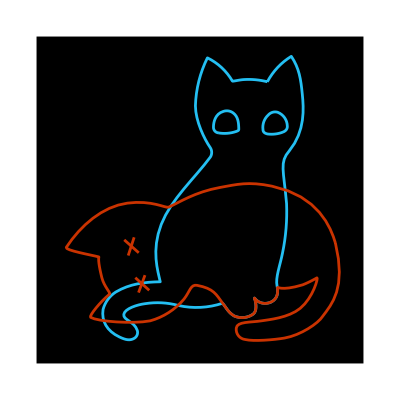

```mathematica
Block[{asset},
asset=<|"alive"->JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{39.26,60.69},{40.54,63.09},{42.44,65.11},{44.76,66.53},{46.59,63.73},{46.93,61.34},{47.28,57.83},{47.59,54.7},{48.02,49.41},{44.28,44.83},{42.,42.23},{43.,40.47},{43.67,32.74},{43.82,28.96},{43.52,25.17},{42.75,21.46},{42.2,18.6},{41.06,15.73},{41.49,13.84},{41.82,12.37},{41.60,10.89},{40.14,10.17},{39.94,10.07},{39.72,9.993},{39.49,9.95},{38.3,9.636},{37.04,10.08},{36.31,11.07},{36.74,9.83},{36.86,8.07},{36.06,7.43},{34.78,6.503},{33.1,6.328},{31.65,6.97},{30.32,7.77},{30.,8.63},{29.,9.89},{25.73,8.803},{22.22,8.623},{18.86,9.37},{16.36,10.05},{13.75,10.19},{11.19,9.78},{9.466,9.568},{6.53,8.66},{6.33,7.33},{6.13,6.},{8.73,5.8},{9.42,3.65},{9.65,2.923},{9.32,2.136},{8.64,1.79},{7.78,1.34},{6.93,1.37},{5.3,2.16},{2.43,3.53},{1.17,5.82},{1.57,8.46},{2.013,10.11},{3.054,11.54},{4.49,12.46},{7.73,14.38},{11.14,14.75},{14.69,14.81},{14.17,17.21},{12.57,21.94},{14.92,27.98},{17.17,33.76},{22.61,38.57},{26.2,43.44},{26.61,44.11},{26.59,44.97},{26.14,45.62},{24.83,47.51},{22.77,51.69},{22.76,55.18},{22.87,59.},{23.81,62.76},{25.51,66.18},{27.91,65.01},{29.9,63.16},{31.24,60.85},{31.29,60.74},{32.85,61.14},{33.87,61.2},{35.68,61.31},{37.5,61.14},{39.26,60.69}},{{28.,48.97},{27.33,49.06},{26.85,49.66},{26.9,50.34},{26.9,51.34},{27.26,53.34},{29.15,53.89},{29.93,54.17},{30.81,54.03},{31.46,53.51},{32.54,52.68},{32.66,51.37},{32.7,50.08},{32.7,49.62},{32.81,49.54},{32.05,49.27},{30.75,48.84},{29.35,48.73},{28.,48.97}},{{42.77,49.12},{43.86,49.52},{43.86,50.28},{43.84,50.53},{43.81,51.94},{42.94,53.19},{41.62,53.7},{40.83,53.92},{39.99,53.67},{39.45,53.05},{38.53,52.2},{38.09,50.95},{38.26,49.71},{38.26,49.26},{38.54,48.87},{39.33,48.71},{40.49,48.57},{41.67,48.71},{42.77,49.12}}}],
"dead"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{63.26,23.81},{65.78,13.39},{62.4,9.81},{60.34,7.03},{59.34,5.41},{55.29,2.68},{51.58,2.03},{49.23,1.63},{44.48,1.22},{42.58,1.69},{41.29,1.834},{40.36,2.997},{40.51,4.287},{40.51,4.298},{40.51,4.309},{40.51,4.32},{40.69,5.87},{43.78,5.58},{46.3,5.98},{47.99,6.25},{52.47,6.65},{55.17,8.84},{58.17,11.31},{59.39,16.},{59.01,15.84},{57.96,15.23},{56.87,14.69},{55.75,14.24},{50.55,12.68},{49.92,13.94},{49.96,13.55},{50.06,12.7},{50.19,10.69},{47.88,10.07},{46.67,9.767},{45.42,10.2},{44.69,11.2},{45.11,9.906},{45.28,8.213},{44.39,7.521},{43.17,6.64},{41.49,6.45},{40.04,7.09},{38.68,7.94},{38.37,8.746},{37.39,10.02},{35.86,12.06},{35.4,13.38},{31.52,14.12},{30.03,14.41},{29.91,12.75},{28.52,10.97},{26.49,8.55},{23.77,6.806},{20.73,5.97},{16.73,5.23},{8.64,5.81},{7.1,6.78},{6.64,7.06},{9.44,10.5},{11.45,12.1},{11.77,12.35},{10.19,13.82},{9.67,15.88},{9.33,17.27},{8.76,19.72},{8.99,20.64},{7.42,21.06},{1.09,22.17},{1.52,22.84},{4.79,27.84},{9.83,32.23},{15.52,32.98},{21.21,33.73},{24.3,31.76},{25.,32.06},{27.29,33.06},{31.,35.55},{36.8,36.58},{40.6,37.26},{43.22,38.02},{48.71,36.87},{59.39,34.65},{62.23,27.36},{63.26,23.81}}}],
JoinedCurve[{{{0,2,0}},{{0,2,0}},{{0,2,0}},{{0,2,0}}},{{{14.81,24.56},{18.14,21.59}},{{17.08,25.14},{15.72,20.96}},{{17.35,15.88},{20.54,12.98}},{{19.57,16.46},{18.09,12.46}}}]},
"neuron"->JoinedCurve[{{{1,4,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{56.68,24.8},{56.42,25.32},{56.2,25.85},{56.15,27.5},{56.36,33.72},{48.49,40.15},{44.9,42.79},{44.82,42.85},{43.6,43.73},{39.82,46.45},{23.34,53.72},{18.88,61.89},{16.3,67.35},{15.76,74.57},{16.68,81.33},{17.05,83.17},{18.08,83.79},{19.14,84.3},{21.58,85.51},{24.95,85.16},{29.36,82.59},{26.81,86.74},{24.54,87.83},{24.54,91.59},{24.54,96.12},{28.02,97.79},{31.25,100.9},{29.01,99.96},{22.49,98.04},{20.38,100.},{17.66,102.6},{18.15,105.7},{17.57,109.3},{16.36,106.4},{15.4,101.7},{12.14,100.2},{9.07,98.87},{4.79,100.8},{1.91,102.2},{4.26,99.36},{7.91,95.77},{7.73,92.51},{7.45,87.83},{3.57,86.18},{1.53,83.37},{4.09,84.37},{7.89,86.24},{10.73,85.09},{12.5,84.38},{13.47,82.81},{13.39,80.39},{13.46,73.91},{13.68,67.62},{16.68,61.52},{20.91,52.49},{38.6,45.1},{42.57,42.24},{43.77,41.37},{43.85,41.31},{46.98,39.01},{54.52,33.63},{54.45,27.7},{54.43,27.16},{54.41,26.77},{54.36,26.4},{54.33,26.03},{54.33,25.75},{54.27,25.47},{54.22,25.21},{54.17,24.95},{54.14,24.93},{54.09,24.79},{53.82,24.32},{53.49,23.9},{53.09,23.53},{52.63,23.24},{52.08,23.11},{51.54,23.17},{50.36,23.35},{49.54,24.9},{48.89,26.04},{48.27,27.39},{47.17,28.45},{45.81,29.04},{45.74,29.04},{45.62,29.04},{44.67,29.94},{43.5,30.59},{42.24,30.93},{42.06,30.26},{43.,30.01},{43.88,29.57},{44.65,28.97},{44.18,28.85},{43.71,28.73},{43.26,28.6},{43.09,28.56},{42.96,28.43},{42.93,28.26},{42.91,28.12},{42.97,27.97},{43.09,27.89},{43.5,27.89},{43.5,27.98},{43.97,28.12},{44.44,28.24},{44.91,28.35},{45.33,28.33},{45.74,28.23},{46.12,28.05},{46.93,27.58},{47.12,26.96},{47.75,26.05},{47.43,26.16},{47.09,26.21},{46.75,26.21},{45.82,26.67},{44.79,26.9},{43.75,26.87},{43.75,26.19},{44.52,26.21},{45.28,26.07},{45.99,25.79},{45.41,25.56},{44.84,25.29},{44.3,24.98},{44.65,24.39},{45.28,24.76},{45.95,25.06},{46.65,25.29},{47.45,25.27},{48.2,24.93},{48.75,24.35},{49.23,23.48},{49.92,22.73},{50.75,22.18},{50.69,22.18},{50.01,22.16},{49.34,22.25},{48.69,22.45},{47.61,23.07},{46.35,23.34},{45.11,23.22},{45.18,22.54},{46.03,22.62},{46.88,22.5},{47.67,22.18},{46.94,21.9},{46.24,21.54},{45.59,21.1},{45.97,20.53},{46.72,21.03},{47.55,21.42},{48.42,21.68},{49.11,21.42},{49.84,21.26},{50.57,21.18},{50.54,21.13},{50.51,21.08},{50.49,21.02},{50.31,20.29},{49.81,19.69},{49.13,19.37},{48.25,19.29},{47.68,18.93},{46.93,18.18},{46.25,17.69},{46.64,17.12},{47.2,17.52},{47.75,17.95},{48.27,18.4},{48.35,18.03},{48.4,17.64},{48.4,17.26},{48.41,16.73},{48.23,16.22},{47.9,15.81},{48.4,15.34},{48.85,15.87},{49.09,16.55},{49.08,17.25},{49.05,17.69},{49.12,18.13},{49.27,18.54},{50.43,19.03},{51.3,20.04},{51.6,21.27},{51.73,21.88},{52.6,21.9},{53.69,22.58},{54.78,23.26},{55.36,24.18},{55.42,24.03},{55.81,23.32},{56.12,22.57},{56.35,21.79},{56.49,20.24},{56.31,18.67},{55.8,17.19},{55.55,16.28},{55.17,15.41},{54.68,14.6},{54.43,14.27},{54.08,14.03},{53.68,13.9},{53.43,13.82},{52.55,13.73},{52.43,13.71},{52.3,13.69},{52.16,13.65},{52.04,13.59},{51.69,13.59},{50.82,13.74},{49.98,13.99},{49.18,14.36},{48.53,14.49},{47.91,14.67},{47.31,14.9},{46.73,15.17},{46.66,15.17},{46.38,14.54},{46.46,14.54},{47.,14.29},{47.55,14.07},{48.12,13.89},{47.93,13.76},{47.72,13.65},{47.51,13.56},{47.03,13.35},{46.56,13.14},{46.84,12.51},{47.31,12.72},{47.78,12.93},{48.13,13.06},{48.45,13.26},{48.73,13.52},{49.53,13.17},{50.36,12.91},{51.22,12.74},{50.5,12.08},{49.61,11.63},{48.65,11.45},{47.84,11.49},{47.04,11.64},{46.27,11.89},{46.04,11.24},{46.69,11.03},{47.36,10.88},{48.04,10.81},{47.82,10.61},{47.58,10.43},{47.33,10.27},{47.09,10.12},{46.83,9.986},{46.57,9.87},{45.91,9.54},{46.23,8.93},{46.87,9.25},{47.16,9.375},{47.44,9.525},{47.71,9.7},{48.13,9.976},{48.51,10.31},{48.84,10.7},{49.56,10.85},{50.56,11.13},{51.47,11.67},{52.2,12.41},{53.01,12.82},{53.44,12.84},{53.87,12.89},{54.3,12.97},{53.9,11.7},{53.33,10.5},{52.6,9.39},{52.16,8.851},{51.62,8.411},{51.,8.1},{50.19,7.79},{49.34,7.611},{48.47,7.57},{47.86,7.57},{47.42,7.647},{46.97,7.7},{46.52,7.73},{45.52,7.84},{45.43,7.16},{46.43,7.05},{46.76,7.05},{47.11,6.99},{47.43,6.94},{47.25,6.8},{47.,6.62},{46.65,6.39},{46.53,6.31},{46.37,6.22},{46.2,6.13},{46.03,6.04},{45.71,5.85},{45.52,5.71},{45.93,5.16},{46.09,5.27},{46.32,5.4},{46.54,5.53},{47.03,5.82},{47.44,6.073},{47.83,6.368},{48.18,6.7},{48.91,6.654},{49.65,6.714},{50.37,6.88},{50.11,6.263},{49.69,5.728},{49.15,5.33},{48.47,4.789},{47.7,4.372},{46.87,4.1},{46.55,4.1},{46.09,4.1},{45.18,4.1},{44.55,4.1},{44.2,4.1},{44.2,3.41},{46.,3.41},{45.79,3.081},{45.54,2.779},{45.26,2.51},{44.95,2.237},{44.62,1.996},{44.26,1.79},{44.02,1.65},{43.57,1.43},{43.49,1.36},{43.7,0.87},{43.77,0.93},{44.63,1.35},{44.85,1.45},{45.59,1.814},{46.21,2.388},{46.63,3.1},{47.75,3.397},{48.81,3.914},{49.73,4.62},{50.59,5.237},{51.24,6.103},{51.59,7.1},{52.35,7.622},{53.02,8.256},{53.59,8.98},{54.44,10.31},{55.05,11.78},{55.38,13.33},{55.38,13.33},{56.51,15.66},{56.85,16.56},{57.41,17.89},{57.69,19.32},{57.68,20.77},{57.59,22.16},{57.25,23.53},{56.68,24.8}}}]|>;
Graphics[{{Black,Rectangle[{-50,-15},{25,60
}]},{AbsoluteThickness[2],Translate[{Cyan,asset["alive"]},{-36.31,-11.07}],Translate[{{Red,asset["dead"]}},{-44.69,-11.20}]}}]]
```

```mathematica
Block[{asset,spin},
asset=<|"alive"->JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{39.26,60.69},{40.54,63.09},{42.44,65.11},{44.76,66.53},{46.59,63.73},{46.93,61.34},{47.28,57.83},{47.59,54.7},{48.02,49.41},{44.28,44.83},{42.,42.23},{43.,40.47},{43.67,32.74},{43.82,28.96},{43.52,25.17},{42.75,21.46},{42.2,18.6},{41.06,15.73},{41.49,13.84},{41.82,12.37},{41.60,10.89},{40.14,10.17},{39.94,10.07},{39.72,9.993},{39.49,9.95},{38.3,9.636},{37.04,10.08},{36.31,11.07},{36.74,9.83},{36.86,8.07},{36.06,7.43},{34.78,6.503},{33.1,6.328},{31.65,6.97},{30.32,7.77},{30.,8.63},{29.,9.89},{25.73,8.803},{22.22,8.623},{18.86,9.37},{16.36,10.05},{13.75,10.19},{11.19,9.78},{9.466,9.568},{6.53,8.66},{6.33,7.33},{6.13,6.},{8.73,5.8},{9.42,3.65},{9.65,2.923},{9.32,2.136},{8.64,1.79},{7.78,1.34},{6.93,1.37},{5.3,2.16},{2.43,3.53},{1.17,5.82},{1.57,8.46},{2.013,10.11},{3.054,11.54},{4.49,12.46},{7.73,14.38},{11.14,14.75},{14.69,14.81},{14.17,17.21},{12.57,21.94},{14.92,27.98},{17.17,33.76},{22.61,38.57},{26.2,43.44},{26.61,44.11},{26.59,44.97},{26.14,45.62},{24.83,47.51},{22.77,51.69},{22.76,55.18},{22.87,59.},{23.81,62.76},{25.51,66.18},{27.91,65.01},{29.9,63.16},{31.24,60.85},{31.29,60.74},{32.85,61.14},{33.87,61.2},{35.68,61.31},{37.5,61.14},{39.26,60.69}},{{28.,48.97},{27.33,49.06},{26.85,49.66},{26.9,50.34},{26.9,51.34},{27.26,53.34},{29.15,53.89},{29.93,54.17},{30.81,54.03},{31.46,53.51},{32.54,52.68},{32.66,51.37},{32.7,50.08},{32.7,49.62},{32.81,49.54},{32.05,49.27},{30.75,48.84},{29.35,48.73},{28.,48.97}},{{42.77,49.12},{43.86,49.52},{43.86,50.28},{43.84,50.53},{43.81,51.94},{42.94,53.19},{41.62,53.7},{40.83,53.92},{39.99,53.67},{39.45,53.05},{38.53,52.2},{38.09,50.95},{38.26,49.71},{38.26,49.26},{38.54,48.87},{39.33,48.71},{40.49,48.57},{41.67,48.71},{42.77,49.12}}}],
"dead"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{63.26,23.81},{65.78,13.39},{62.4,9.81},{60.34,7.03},{59.34,5.41},{55.29,2.68},{51.58,2.03},{49.23,1.63},{44.48,1.22},{42.58,1.69},{41.29,1.834},{40.36,2.997},{40.51,4.287},{40.51,4.298},{40.51,4.309},{40.51,4.32},{40.69,5.87},{43.78,5.58},{46.3,5.98},{47.99,6.25},{52.47,6.65},{55.17,8.84},{58.17,11.31},{59.39,16.},{59.01,15.84},{57.96,15.23},{56.87,14.69},{55.75,14.24},{50.55,12.68},{49.92,13.94},{49.96,13.55},{50.06,12.7},{50.19,10.69},{47.88,10.07},{46.67,9.767},{45.42,10.2},{44.69,11.2},{45.11,9.906},{45.28,8.213},{44.39,7.521},{43.17,6.64},{41.49,6.45},{40.04,7.09},{38.68,7.94},{38.37,8.746},{37.39,10.02},{35.86,12.06},{35.4,13.38},{31.52,14.12},{30.03,14.41},{29.91,12.75},{28.52,10.97},{26.49,8.55},{23.77,6.806},{20.73,5.97},{16.73,5.23},{8.64,5.81},{7.1,6.78},{6.64,7.06},{9.44,10.5},{11.45,12.1},{11.77,12.35},{10.19,13.82},{9.67,15.88},{9.33,17.27},{8.76,19.72},{8.99,20.64},{7.42,21.06},{1.09,22.17},{1.52,22.84},{4.79,27.84},{9.83,32.23},{15.52,32.98},{21.21,33.73},{24.3,31.76},{25.,32.06},{27.29,33.06},{31.,35.55},{36.8,36.58},{40.6,37.26},{43.22,38.02},{48.71,36.87},{59.39,34.65},{62.23,27.36},{63.26,23.81}}}],
JoinedCurve[{{{0,2,0}},{{0,2,0}},{{0,2,0}},{{0,2,0}}},{{{14.81,24.56},{18.14,21.59}},{{17.08,25.14},{15.72,20.96}},{{17.35,15.88},{20.54,12.98}},{{19.57,16.46},{18.09,12.46}}}]},
"neuron"->JoinedCurve[{{{1,4,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{56.68,24.8},{56.42,25.32},{56.2,25.85},{56.15,27.5},{56.36,33.72},{48.49,40.15},{44.9,42.79},{44.82,42.85},{43.6,43.73},{39.82,46.45},{23.34,53.72},{18.88,61.89},{16.3,67.35},{15.76,74.57},{16.68,81.33},{17.05,83.17},{18.08,83.79},{19.14,84.3},{21.58,85.51},{24.95,85.16},{29.36,82.59},{26.81,86.74},{24.54,87.83},{24.54,91.59},{24.54,96.12},{28.02,97.79},{31.25,100.9},{29.01,99.96},{22.49,98.04},{20.38,100.},{17.66,102.6},{18.15,105.7},{17.57,109.3},{16.36,106.4},{15.4,101.7},{12.14,100.2},{9.07,98.87},{4.79,100.8},{1.91,102.2},{4.26,99.36},{7.91,95.77},{7.73,92.51},{7.45,87.83},{3.57,86.18},{1.53,83.37},{4.09,84.37},{7.89,86.24},{10.73,85.09},{12.5,84.38},{13.47,82.81},{13.39,80.39},{13.46,73.91},{13.68,67.62},{16.68,61.52},{20.91,52.49},{38.6,45.1},{42.57,42.24},{43.77,41.37},{43.85,41.31},{46.98,39.01},{54.52,33.63},{54.45,27.7},{54.43,27.16},{54.41,26.77},{54.36,26.4},{54.33,26.03},{54.33,25.75},{54.27,25.47},{54.22,25.21},{54.17,24.95},{54.14,24.93},{54.09,24.79},{53.82,24.32},{53.49,23.9},{53.09,23.53},{52.63,23.24},{52.08,23.11},{51.54,23.17},{50.36,23.35},{49.54,24.9},{48.89,26.04},{48.27,27.39},{47.17,28.45},{45.81,29.04},{45.74,29.04},{45.62,29.04},{44.67,29.94},{43.5,30.59},{42.24,30.93},{42.06,30.26},{43.,30.01},{43.88,29.57},{44.65,28.97},{44.18,28.85},{43.71,28.73},{43.26,28.6},{43.09,28.56},{42.96,28.43},{42.93,28.26},{42.91,28.12},{42.97,27.97},{43.09,27.89},{43.5,27.89},{43.5,27.98},{43.97,28.12},{44.44,28.24},{44.91,28.35},{45.33,28.33},{45.74,28.23},{46.12,28.05},{46.93,27.58},{47.12,26.96},{47.75,26.05},{47.43,26.16},{47.09,26.21},{46.75,26.21},{45.82,26.67},{44.79,26.9},{43.75,26.87},{43.75,26.19},{44.52,26.21},{45.28,26.07},{45.99,25.79},{45.41,25.56},{44.84,25.29},{44.3,24.98},{44.65,24.39},{45.28,24.76},{45.95,25.06},{46.65,25.29},{47.45,25.27},{48.2,24.93},{48.75,24.35},{49.23,23.48},{49.92,22.73},{50.75,22.18},{50.69,22.18},{50.01,22.16},{49.34,22.25},{48.69,22.45},{47.61,23.07},{46.35,23.34},{45.11,23.22},{45.18,22.54},{46.03,22.62},{46.88,22.5},{47.67,22.18},{46.94,21.9},{46.24,21.54},{45.59,21.1},{45.97,20.53},{46.72,21.03},{47.55,21.42},{48.42,21.68},{49.11,21.42},{49.84,21.26},{50.57,21.18},{50.54,21.13},{50.51,21.08},{50.49,21.02},{50.31,20.29},{49.81,19.69},{49.13,19.37},{48.25,19.29},{47.68,18.93},{46.93,18.18},{46.25,17.69},{46.64,17.12},{47.2,17.52},{47.75,17.95},{48.27,18.4},{48.35,18.03},{48.4,17.64},{48.4,17.26},{48.41,16.73},{48.23,16.22},{47.9,15.81},{48.4,15.34},{48.85,15.87},{49.09,16.55},{49.08,17.25},{49.05,17.69},{49.12,18.13},{49.27,18.54},{50.43,19.03},{51.3,20.04},{51.6,21.27},{51.73,21.88},{52.6,21.9},{53.69,22.58},{54.78,23.26},{55.36,24.18},{55.42,24.03},{55.81,23.32},{56.12,22.57},{56.35,21.79},{56.49,20.24},{56.31,18.67},{55.8,17.19},{55.55,16.28},{55.17,15.41},{54.68,14.6},{54.43,14.27},{54.08,14.03},{53.68,13.9},{53.43,13.82},{52.55,13.73},{52.43,13.71},{52.3,13.69},{52.16,13.65},{52.04,13.59},{51.69,13.59},{50.82,13.74},{49.98,13.99},{49.18,14.36},{48.53,14.49},{47.91,14.67},{47.31,14.9},{46.73,15.17},{46.66,15.17},{46.38,14.54},{46.46,14.54},{47.,14.29},{47.55,14.07},{48.12,13.89},{47.93,13.76},{47.72,13.65},{47.51,13.56},{47.03,13.35},{46.56,13.14},{46.84,12.51},{47.31,12.72},{47.78,12.93},{48.13,13.06},{48.45,13.26},{48.73,13.52},{49.53,13.17},{50.36,12.91},{51.22,12.74},{50.5,12.08},{49.61,11.63},{48.65,11.45},{47.84,11.49},{47.04,11.64},{46.27,11.89},{46.04,11.24},{46.69,11.03},{47.36,10.88},{48.04,10.81},{47.82,10.61},{47.58,10.43},{47.33,10.27},{47.09,10.12},{46.83,9.986},{46.57,9.87},{45.91,9.54},{46.23,8.93},{46.87,9.25},{47.16,9.375},{47.44,9.525},{47.71,9.7},{48.13,9.976},{48.51,10.31},{48.84,10.7},{49.56,10.85},{50.56,11.13},{51.47,11.67},{52.2,12.41},{53.01,12.82},{53.44,12.84},{53.87,12.89},{54.3,12.97},{53.9,11.7},{53.33,10.5},{52.6,9.39},{52.16,8.851},{51.62,8.411},{51.,8.1},{50.19,7.79},{49.34,7.611},{48.47,7.57},{47.86,7.57},{47.42,7.647},{46.97,7.7},{46.52,7.73},{45.52,7.84},{45.43,7.16},{46.43,7.05},{46.76,7.05},{47.11,6.99},{47.43,6.94},{47.25,6.8},{47.,6.62},{46.65,6.39},{46.53,6.31},{46.37,6.22},{46.2,6.13},{46.03,6.04},{45.71,5.85},{45.52,5.71},{45.93,5.16},{46.09,5.27},{46.32,5.4},{46.54,5.53},{47.03,5.82},{47.44,6.073},{47.83,6.368},{48.18,6.7},{48.91,6.654},{49.65,6.714},{50.37,6.88},{50.11,6.263},{49.69,5.728},{49.15,5.33},{48.47,4.789},{47.7,4.372},{46.87,4.1},{46.55,4.1},{46.09,4.1},{45.18,4.1},{44.55,4.1},{44.2,4.1},{44.2,3.41},{46.,3.41},{45.79,3.081},{45.54,2.779},{45.26,2.51},{44.95,2.237},{44.62,1.996},{44.26,1.79},{44.02,1.65},{43.57,1.43},{43.49,1.36},{43.7,0.87},{43.77,0.93},{44.63,1.35},{44.85,1.45},{45.59,1.814},{46.21,2.388},{46.63,3.1},{47.75,3.397},{48.81,3.914},{49.73,4.62},{50.59,5.237},{51.24,6.103},{51.59,7.1},{52.35,7.622},{53.02,8.256},{53.59,8.98},{54.44,10.31},{55.05,11.78},{55.38,13.33},{55.38,13.33},{56.51,15.66},{56.85,16.56},{57.41,17.89},{57.69,19.32},{57.68,20.77},{57.59,22.16},{57.25,23.53},{56.68,24.8}}}]|>;
spin[h_,w_,b_]:=
Polygon[{{-w,-h},{w,-h},{w,b},{2w,b},{0,h},{-2w,b},{-w,b}}];
Graphics[{
(*background*){Raster[{(1+Tanh[Range[-10,10,0.02]])/2},{{-100,-20},{100,120}}]},
(*quantum world*)Translate[{
(*qubit*)Translate[{
(*atomic shell*){Yellow,Rotate[Circle[{0,0},{8,16}],2 π#/3]&/@ Range[3]},
(*spin*)Block[{h=5,w=2,b=0},
{Opacity[0.3],
Translate[{EdgeForm[Pink],Pink,spin[h,w,b]},{w/2,h/2}],
Translate[{EdgeForm[Cyan],Cyan,spin[-h,w,-b]},{-w/2,-h/2}]}]},{-8,95}],
(*Schrodinger cat*){
(*alive cat*)Translate[{Pink,{Opacity[0.3],FilledCurve@@asset["alive"]},asset["alive"]},{-36.31,-11.07}],
(*dead cat*)Translate[{Cyan,{Opacity[0.3],FilledCurve@@First@asset["dead"]},asset["dead"]},{-44.69,-11.20}]}},{-40,0}],
(*classical world*)Translate[{
(*eye*){Circle[{0,0},27],{Gray,Disk[{-12,0},12]},{Black,Disk[{-14,0},6]},{White,Translate[Rotate[Disk[{0,0},{2,3}],π/4],ReIm[-14+6Exp[ⅈ π/4]]]}},
(*neoron*)Translate[{
(*cell*){EdgeForm[Black],GrayLevel[0.9],FilledCurve@@asset["neuron"]},
(*neuclear*){Gray,Disk[{16,92.5},3.5]}},{-21,-15}]},{45,20}]},Frame->True]]
```

-Graphics-

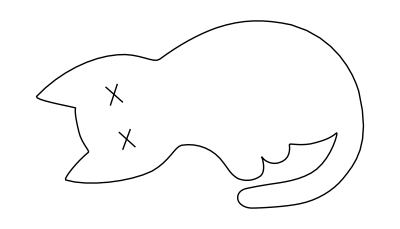

```mathematica
Graphics[{JoinedCurve[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{63.33, 23.69}, {65.85, 13.27}, {62.47, 9.69}, {60.32, 6.94}, {58.36, 4.55}, {55.33, 2.76}, {52.03, 2.09}, {49.30, 1.51}, {44.55, 1.27}, {42.87, 1.26}, {41.69, 1.25}, {40.37, 1.88}, {40.15, 2.94}, {39.96, 4.10}, {40.80, 4.80}, {41.78, 5.02}, {42.96, 5.27}, {43.85, 5.46}, {46.37, 5.86}, {48.06, 6.13}, {52.54, 6.53}, {55.24, 8.72}, {58.24, 11.19}, {59.44, 15.95}, {59.08, 15.72}, {58.34, 15.07}, {57.26, 14.32}, {54.13, 13.61}, {51.60, 13.19}, {49.99, 13.82}, {50.03, 13.43}, {50.13, 12.58}, {50.26, 10.57}, {47.95, 9.95}, {46.74, 9.65}, {45.49, 10.08}, {44.76, 11.08}, {45.18, 9.79}, {45.35, 8.09}, {44.46, 7.40}, {43.24, 6.52}, {41.56, 6.33}, {40.11, 6.97}, {38.75, 7.82}, {38.44, 8.63}, {37.46, 9.90}, {35.63, 12.57}, {32.49, 13.86}, {29.38, 13.34}, {28.01, 13.02}, {27.14, 10.29}, {23.69, 8.35}, {19.40, 6.25}, {11.36, 5.37}, {7.17, 6.66}, {6.71, 6.94}, {9.51, 10.38}, {11.52, 11.98}, {11.84, 12.23}, {10.26, 13.70}, {9.74, 15.76}, {9.40, 17.15}, {8.83, 19.60}, {9.06, 20.52}, {7.49, 20.94}, {1.16, 22.05}, {1.59, 22.72}, {6.06, 27.46}, {12.13, 30.36}, {17.08, 30.73}, {21.24, 31.15}, {24.02, 29.00}, {25.18, 29.88}, {28.92, 32.66}, {32.67, 34.71}, {36.06, 35.91}, {41.02, 37.57}, {45.23, 37.61}, {50.40, 36.49}, {58.91, 34.11}, {62.30, 27.24}, {63.33, 23.69}}}], JoinedCurve[{{{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}}, {{{14.81, 24.56}, {18.14, 21.59}}, {{17.08, 25.14}, {15.72, 20.96}}, {{17.35, 15.88}, {20.54, 12.98}}, {{19.57, 16.46}, {18.09, 12.46}}}]}]
```

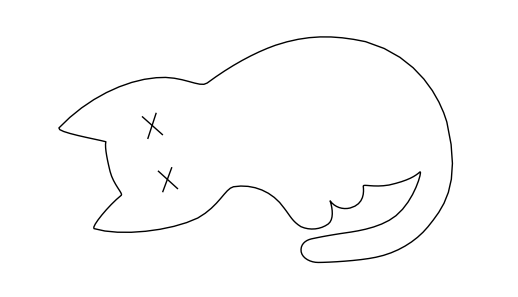
```mathematica
ToString[DecimalForm[First@#,{4,2}]]&@
-Graphics-
```

{JoinedCurve[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{63.33, 23.69}, {65.85, 13.27}, {62.47, 9.69}, {60.32, 6.94}, {58.36, 4.55}, {55.33, 2.76}, {52.03, 2.09}, {49.30, 1.51}, {44.55, 1.27}, {42.87, 1.26}, {41.69, 1.25}, {40.37, 1.88}, {40.15, 2.94}, {39.96, 4.10}, {40.80, 4.80}, {41.78, 5.02}, {42.96, 5.27}, {43.85, 5.46}, {46.37, 5.86}, {48.06, 6.13}, {52.54, 6.53}, {55.24, 8.72}, {58.24, 11.19}, {59.44, 15.95}, {59.08, 15.72}, {58.34, 15.07}, {57.26, 14.32}, {54.13, 13.61}, {51.60, 13.19}, {49.99, 13.82}, {50.03, 13.43}, {50.13, 12.58}, {50.26, 10.57}, {47.95, 9.95}, {46.74, 9.65}, {45.49, 10.08}, {44.76, 11.08}, {45.18, 9.79}, {45.35, 8.09}, {44.46, 7.40}, {43.24, 6.52}, {41.56, 6.33}, {40.11, 6.97}, {38.75, 7.82}, {38.44, 8.63}, {37.46, 9.90}, {35.63, 12.57}, {32.49, 13.86}, {29.38, 13.34}, {28.01, 13.02}, {27.14, 10.29}, {23.69, 8.35}, {19.40, 6.25}, {11.36, 5.37}, {7.17, 6.66}, {6.71, 6.94}, {9.51, 10.38}, {11.52, 11.98}, {11.84, 12.23}, {10.26, 13.70}, {9.74, 15.76}, {9.40, 17.15}, {8.83, 19.60}, {9.06, 20.52}, {7.49, 20.94}, {1.16, 22.05}, {1.59, 22.72}, {6.06, 27.46}, {12.13, 30.36}, {17.08, 30.73}, {21.24, 31.15}, {24.02, 29.00}, {25.18, 29.88}, {28.92, 32.66}, {32.67, 34.71}, {36.06, 35.91}, {41.02, 37.57}, {45.23, 37.61}, {50.40, 36.49}, {58.91, 34.11}, {62.30, 27.24}, {63.33, 23.69}}}], JoinedCurve[{{{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}, {{0, 2, 0}}}, {{{14.81, 24.56}, {18.14, 21.59}}, {{17.08, 25.14}, {15.72, 20.96}}, {{17.35, 15.88}, {20.54, 12.98}}, {{19.57, 16.46}, {18.09, 12.46}}}]}

```mathematica
Block[{asset,spin,opblend,wave,opsty},
asset=<|"alive"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}},{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{39.26,60.69},{40.54,63.09},{42.44,65.11},{44.76,66.53},{46.59,63.73},{46.93,61.34},{47.28,57.83},{47.59,54.7},{48.02,49.41},{44.28,44.83},{42.,42.23},{43.,40.47},{43.67,32.74},{43.82,28.96},{43.52,25.17},{42.75,21.46},{42.2,18.6},{41.06,15.73},{41.49,13.84},{41.82,12.37},{41.60,10.89},{40.14,10.17},{39.94,10.07},{39.72,9.993},{39.49,9.95},{38.3,9.636},{37.04,10.08},{36.31,11.07},{36.74,9.83},{36.86,8.07},{36.06,7.43},{34.78,6.503},{33.1,6.328},{31.65,6.97},{30.32,7.77},{30.,8.63},{29.,9.89},{25.73,8.803},{22.22,8.623},{18.86,9.37},{16.36,10.05},{13.75,10.19},{11.19,9.78},{9.466,9.568},{6.53,8.66},{6.33,7.33},{6.13,6.},{8.73,5.8},{9.42,3.65},{9.65,2.923},{9.32,2.136},{8.64,1.79},{7.78,1.34},{6.93,1.37},{5.3,2.16},{2.43,3.53},{1.17,5.82},{1.57,8.46},{2.013,10.11},{3.054,11.54},{4.49,12.46},{7.73,14.38},{11.14,14.75},{14.69,14.81},{14.17,17.21},{12.57,21.94},{14.92,27.98},{17.17,33.76},{22.61,38.57},{26.2,43.44},{26.61,44.11},{26.59,44.97},{26.14,45.62},{24.83,47.51},{22.77,51.69},{22.76,55.18},{22.87,59.},{23.81,62.76},{25.51,66.18},{27.91,65.01},{29.9,63.16},{31.24,60.85},{31.29,60.74},{32.85,61.14},{33.87,61.2},{35.68,61.31},{37.5,61.14},{39.26,60.69}},{{28.,48.97},{27.33,49.06},{26.85,49.66},{26.9,50.34},{26.9,51.34},{27.26,53.34},{29.15,53.89},{29.93,54.17},{30.81,54.03},{31.46,53.51},{32.54,52.68},{32.66,51.37},{32.7,50.08},{32.7,49.62},{32.81,49.54},{32.05,49.27},{30.75,48.84},{29.35,48.73},{28.,48.97}},{{42.77,49.12},{43.86,49.52},{43.86,50.28},{43.84,50.53},{43.81,51.94},{42.94,53.19},{41.62,53.7},{40.83,53.92},{39.99,53.67},{39.45,53.05},{38.53,52.2},{38.09,50.95},{38.26,49.71},{38.26,49.26},{38.54,48.87},{39.33,48.71},{40.49,48.57},{41.67,48.71},{42.77,49.12}}}]},
"dead"->{JoinedCurve[{{{1,4,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{63.26,23.81},{65.78,13.39},{62.4,9.81},{60.34,7.03},{59.34,5.41},{55.29,2.68},{51.58,2.03},{49.23,1.63},{44.48,1.22},{42.58,1.69},{41.29,1.834},{40.36,2.997},{40.51,4.287},{40.51,4.298},{40.51,4.309},{40.51,4.32},{40.69,5.87},{43.78,5.58},{46.3,5.98},{47.99,6.25},{52.47,6.65},{55.17,8.84},{58.17,11.31},{59.39,16.},{59.01,15.84},{57.96,15.23},{56.87,14.69},{55.75,14.24},{50.55,12.68},{49.92,13.94},{49.96,13.55},{50.06,12.7},{50.19,10.69},{47.88,10.07},{46.67,9.767},{45.42,10.2},{44.69,11.2},{45.11,9.906},{45.28,8.213},{44.39,7.521},{43.17,6.64},{41.49,6.45},{40.04,7.09},{38.68,7.94},{38.37,8.746},{37.39,10.02},{35.86,12.06},{35.4,13.38},{31.52,14.12},{30.03,14.41},{29.91,12.75},{28.52,10.97},{26.49,8.55},{23.77,6.806},{20.73,5.97},{16.73,5.23},{8.64,5.81},{7.1,6.78},{6.64,7.06},{9.44,10.5},{11.45,12.1},{11.77,12.35},{10.19,13.82},{9.67,15.88},{9.33,17.27},{8.76,19.72},{8.99,20.64},{7.42,21.06},{1.09,22.17},{1.52,22.84},{4.79,27.84},{9.83,32.23},{15.52,32.98},{21.21,33.73},{24.3,31.76},{25.,32.06},{27.29,33.06},{31.,35.55},{36.8,36.58},{40.6,37.26},{43.22,38.02},{48.71,36.87},{59.39,34.65},{62.23,27.36},{63.26,23.81}}}],
JoinedCurve[{{{0,2,0}},{{0,2,0}},{{0,2,0}},{{0,2,0}}},{{{14.81,24.56},{18.14,21.59}},{{17.08,25.14},{15.72,20.96}},{{17.35,15.88},{20.54,12.98}},{{19.57,16.46},{18.09,12.46}}}]},
"neuron"->JoinedCurve[{{{1,4,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{0,1,0},{0,1,0},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{0,1,0},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3},{1,3,3}}},{{{56.68,24.8},{56.42,25.32},{56.2,25.85},{56.15,27.5},{56.36,33.72},{48.49,40.15},{44.9,42.79},{44.82,42.85},{43.6,43.73},{39.82,46.45},{23.34,53.72},{18.88,61.89},{16.3,67.35},{15.76,74.57},{16.68,81.33},{17.05,83.17},{18.08,83.79},{19.14,84.3},{21.58,85.51},{24.95,85.16},{29.36,82.59},{26.81,86.74},{24.54,87.83},{24.54,91.59},{24.54,96.12},{28.02,97.79},{31.25,100.9},{29.01,99.96},{22.49,98.04},{20.38,100.},{17.66,102.6},{18.15,105.7},{17.57,109.3},{16.36,106.4},{15.4,101.7},{12.14,100.2},{9.07,98.87},{4.79,100.8},{1.91,102.2},{4.26,99.36},{7.91,95.77},{7.73,92.51},{7.45,87.83},{3.57,86.18},{1.53,83.37},{4.09,84.37},{7.89,86.24},{10.73,85.09},{12.5,84.38},{13.47,82.81},{13.39,80.39},{13.46,73.91},{13.68,67.62},{16.68,61.52},{20.91,52.49},{38.6,45.1},{42.57,42.24},{43.77,41.37},{43.85,41.31},{46.98,39.01},{54.52,33.63},{54.45,27.7},{54.43,27.16},{54.41,26.77},{54.36,26.4},{54.33,26.03},{54.33,25.75},{54.27,25.47},{54.22,25.21},{54.17,24.95},{54.14,24.93},{54.09,24.79},{53.82,24.32},{53.49,23.9},{53.09,23.53},{52.63,23.24},{52.08,23.11},{51.54,23.17},{50.36,23.35},{49.54,24.9},{48.89,26.04},{48.27,27.39},{47.17,28.45},{45.81,29.04},{45.74,29.04},{45.62,29.04},{44.67,29.94},{43.5,30.59},{42.24,30.93},{42.06,30.26},{43.,30.01},{43.88,29.57},{44.65,28.97},{44.18,28.85},{43.71,28.73},{43.26,28.6},{43.09,28.56},{42.96,28.43},{42.93,28.26},{42.91,28.12},{42.97,27.97},{43.09,27.89},{43.5,27.89},{43.5,27.98},{43.97,28.12},{44.44,28.24},{44.91,28.35},{45.33,28.33},{45.74,28.23},{46.12,28.05},{46.93,27.58},{47.12,26.96},{47.75,26.05},{47.43,26.16},{47.09,26.21},{46.75,26.21},{45.82,26.67},{44.79,26.9},{43.75,26.87},{43.75,26.19},{44.52,26.21},{45.28,26.07},{45.99,25.79},{45.41,25.56},{44.84,25.29},{44.3,24.98},{44.65,24.39},{45.28,24.76},{45.95,25.06},{46.65,25.29},{47.45,25.27},{48.2,24.93},{48.75,24.35},{49.23,23.48},{49.92,22.73},{50.75,22.18},{50.69,22.18},{50.01,22.16},{49.34,22.25},{48.69,22.45},{47.61,23.07},{46.35,23.34},{45.11,23.22},{45.18,22.54},{46.03,22.62},{46.88,22.5},{47.67,22.18},{46.94,21.9},{46.24,21.54},{45.59,21.1},{45.97,20.53},{46.72,21.03},{47.55,21.42},{48.42,21.68},{49.11,21.42},{49.84,21.26},{50.57,21.18},{50.54,21.13},{50.51,21.08},{50.49,21.02},{50.31,20.29},{49.81,19.69},{49.13,19.37},{48.25,19.29},{47.68,18.93},{46.93,18.18},{46.25,17.69},{46.64,17.12},{47.2,17.52},{47.75,17.95},{48.27,18.4},{48.35,18.03},{48.4,17.64},{48.4,17.26},{48.41,16.73},{48.23,16.22},{47.9,15.81},{48.4,15.34},{48.85,15.87},{49.09,16.55},{49.08,17.25},{49.05,17.69},{49.12,18.13},{49.27,18.54},{50.43,19.03},{51.3,20.04},{51.6,21.27},{51.73,21.88},{52.6,21.9},{53.69,22.58},{54.78,23.26},{55.36,24.18},{55.42,24.03},{55.81,23.32},{56.12,22.57},{56.35,21.79},{56.49,20.24},{56.31,18.67},{55.8,17.19},{55.55,16.28},{55.17,15.41},{54.68,14.6},{54.43,14.27},{54.08,14.03},{53.68,13.9},{53.43,13.82},{52.55,13.73},{52.43,13.71},{52.3,13.69},{52.16,13.65},{52.04,13.59},{51.69,13.59},{50.82,13.74},{49.98,13.99},{49.18,14.36},{48.53,14.49},{47.91,14.67},{47.31,14.9},{46.73,15.17},{46.66,15.17},{46.38,14.54},{46.46,14.54},{47.,14.29},{47.55,14.07},{48.12,13.89},{47.93,13.76},{47.72,13.65},{47.51,13.56},{47.03,13.35},{46.56,13.14},{46.84,12.51},{47.31,12.72},{47.78,12.93},{48.13,13.06},{48.45,13.26},{48.73,13.52},{49.53,13.17},{50.36,12.91},{51.22,12.74},{50.5,12.08},{49.61,11.63},{48.65,11.45},{47.84,11.49},{47.04,11.64},{46.27,11.89},{46.04,11.24},{46.69,11.03},{47.36,10.88},{48.04,10.81},{47.82,10.61},{47.58,10.43},{47.33,10.27},{47.09,10.12},{46.83,9.986},{46.57,9.87},{45.91,9.54},{46.23,8.93},{46.87,9.25},{47.16,9.375},{47.44,9.525},{47.71,9.7},{48.13,9.976},{48.51,10.31},{48.84,10.7},{49.56,10.85},{50.56,11.13},{51.47,11.67},{52.2,12.41},{53.01,12.82},{53.44,12.84},{53.87,12.89},{54.3,12.97},{53.9,11.7},{53.33,10.5},{52.6,9.39},{52.16,8.851},{51.62,8.411},{51.,8.1},{50.19,7.79},{49.34,7.611},{48.47,7.57},{47.86,7.57},{47.42,7.647},{46.97,7.7},{46.52,7.73},{45.52,7.84},{45.43,7.16},{46.43,7.05},{46.76,7.05},{47.11,6.99},{47.43,6.94},{47.25,6.8},{47.,6.62},{46.65,6.39},{46.53,6.31},{46.37,6.22},{46.2,6.13},{46.03,6.04},{45.71,5.85},{45.52,5.71},{45.93,5.16},{46.09,5.27},{46.32,5.4},{46.54,5.53},{47.03,5.82},{47.44,6.073},{47.83,6.368},{48.18,6.7},{48.91,6.654},{49.65,6.714},{50.37,6.88},{50.11,6.263},{49.69,5.728},{49.15,5.33},{48.47,4.789},{47.7,4.372},{46.87,4.1},{46.55,4.1},{46.09,4.1},{45.18,4.1},{44.55,4.1},{44.2,4.1},{44.2,3.41},{46.,3.41},{45.79,3.081},{45.54,2.779},{45.26,2.51},{44.95,2.237},{44.62,1.996},{44.26,1.79},{44.02,1.65},{43.57,1.43},{43.49,1.36},{43.7,0.87},{43.77,0.93},{44.63,1.35},{44.85,1.45},{45.59,1.814},{46.21,2.388},{46.63,3.1},{47.75,3.397},{48.81,3.914},{49.73,4.62},{50.59,5.237},{51.24,6.103},{51.59,7.1},{52.35,7.622},{53.02,8.256},{53.59,8.98},{54.44,10.31},{55.05,11.78},{55.38,13.33},{55.38,13.33},{56.51,15.66},{56.85,16.56},{57.41,17.89},{57.69,19.32},{57.68,20.77},{57.59,22.16},{57.25,23.53},{56.68,24.8}}}]|>;
spin[h_,w_,b_]:=
{JoinedCurve[{Line[{{-w,-h},{w,-h},{w,b},{2w,b},{0,h},{-2w,b},{-w,b},{-w,-h}}]}]};
opblend[gs_,n_:10]:=Flatten[Table[gs,n],1]/.{Opacity[x_]:>Opacity[1-(1-x)^(1/n)]};
wave[{p1_,p2_}]:=Block[{t,n},
t=p2-p1;n=Normalize[{{0,1},{-1,0}}.t];
Line@Table[p1+x t+2Sin[π x](Cos[10π x])n,{x,0,1,0.01}]];
opsty[col_,blk_:0.4,bdy_:0.98]:={col,{Opacity[blk],FilledCurve@@First@#},{Opacity[bdy],#}}&;
Block[{h=5,w=2,b=0},
Graphics[{
(*background*){Block[{x1=-100,x2=100,y1=-30,y2=150},
{(*gradient*)Raster[{(1+Tanh[Range[-10,10,0.02]])/2},{{x1,y1},{x2,y2}}],
(*frame*){Black,Line[{{x1,y1},{x1,y2},{x2,y2},{x2,y1},{x1,y1}}]}}],
(*world labels*){(*Opacity[0.5],*)
(*quantum*){White,Text[Style["Quantum World",Bold,18],{-50,-20}]},
(*classical*){Black,Text[Style["Classical World",Bold,18],{50,-20}]}}},
(*quantum world*)Translate[{
(*qubit*)Translate[{
(*atomic shell*){Yellow,Rotate[Circle[{0,0},{8,16}],2 π#/3]&/@ Range[3]},
(*spin*)
{AbsoluteThickness[1],opblend@{
Translate[opsty[Pink]@spin[h,w,b],{w/2,h/2}],
Translate[opsty[Cyan]@spin[-h,w,-b],{-w/2,-h/2}]}},
(*entanglement*){{Pink,wave[{{5,-20},{10,-40}}]},{Cyan,wave[{{-5,-20},{-10,-40}}]}}},{0,95}],
(*Schrodinger cat*)Translate[opblend@{
(*alive cat*)Translate[opsty[Pink]@asset["alive"],{-36.31,-11.07}],
(*dead cat*)Translate[opsty[Cyan]@asset["dead"],{-44.69,-11.20}]},{10,0}],
(*cat state*)Translate[{
(*cat state*){
(*alive state*)Translate[{
(*spin+cat*){AbsoluteThickness[1],Translate[opsty[Pink]@spin[h,w,b],{-2w-2.5,0}],Translate[Scale[Translate[opsty[Pink]@asset["alive"],{-36.31,-11.07}],0.2,{0,0}],{6,-5}]},(*ket symbol*){White,Line[{-12,#}&/@{-7,7}],Line[{12-0.3Abs[#],#}&/@{-7,0,7}]}},{-18,0}],
(*dead state*)Translate[{
(*spin+cat*){AbsoluteThickness[1],Translate[opsty[Cyan]@spin[-h,-w,-b],{-2w-2.5,0}],Translate[Scale[Translate[opsty[Cyan]@asset["dead"],{-36.31,-11.07}],0.2,{0,0}],{4.5,-1}]},(*ket symbol*){White,Line[{-12,#}&/@{-7,7}],Line[{12-0.3Abs[#],#}&/@{-7,0,7}]}},{18,0}],
(*plus sign*){White,Text[Style["+",18],{0,0}]}},
(*title*){White,Text["Quantum superposition",{0,16}]}},{0,125}]},{-50,0}],
(*classical world*)Translate[{
(*eye*){Circle[{0,0},27],{Gray,Disk[{-12,0},12]},{Black,Disk[{-14,0},6]},{White,Translate[Rotate[Disk[{0,0},{2,3}],π/4],ReIm[-14+6Exp[ⅈ π/4]]]}},
(*neoron*)Translate[{
(*cell*){EdgeForm[Black],GrayLevel[0.9],FilledCurve@@asset["neuron"]},
(*neuclear*){Gray,Disk[{16,92.5},3.5]}},{-21,-15}],
(*emergent classicality*)Translate[{
(*cloud*)Line@Table[{15,10}ReIm[Exp[ⅈ θ]+0.1Exp[10 ⅈ θ]],{θ,0.,2π,0.01π}],
(*spin+cat*){AbsoluteThickness[1],Translate[opsty[Black]@spin[h,w,b],{-2w-2.5,0}],Translate[Scale[Translate[opsty[Black]@asset["alive"],{-36.31,-11.07}],0.2,{0,0}],{6,-5}]},
(*bubbles*){Circle[{-16,-11},4],Circle[{-25,-15},2]},
(*title*){Black,Text["Classical reality",{-5,16}]}},{30,105}]},{45,20}],
(*weak measurement*)Translate[{
(*dotted lines*){AbsoluteThickness[3],Gray,Dotted,Table[Line[{{-14,1.2y},{14,0.8y}}],{y,-20,20,10}]},
(*text*)Translate[Block[{txt=Style["Weak\nmeasurement\nsignals",LineSpacing->{0,14}]},{{Black,Text[txt,ReIm[0.5Exp[ⅈ 2π #/48]]]&/@Range[48]},{White,Text[txt]}}],{0,40}]},{0,20}]},PlotRangePadding->None,ImageSize->360]]]
```

-Graphics-